```mathematica
f[s_,t_]={2+2Cos[t],2*Sin[t],s}
```

{2+2 Cos[t],2 Sin[t],s}

```mathematica
cyl=ParametricPlot3D[f[s,t],{s,-3,3},{t,-3,4},AxesLabel->{X,Y,Z}]
```

-Graphics3D-

```mathematica
plane1=ParametricPlot3D[{x,y,4},{x,0,4},{y,-2,2}]
Show[cyl,plane1,AxesLabel->{x,y,z}]
```

-Graphics3D-

-Graphics3D-

```mathematica
u=Pi/4;
cyl2=ParametricPlot3D[{Cos[u]*(2*Cos[t]+2)-Sin[u]*s,2*Sin[t],Sin[u]*(2*Cos[t]+2)+Cos[u]*s},{s,0,10},{t,0,2Pi}]
plane2=ParametricPlot3D[{x,y,4},{x,-6,4},{y,-2,2}]
Show[cyl2,plane2, AxesLabel->{x,y,z},ViewPoint->{0, -3, 0},BoxRatios->{1,1,1}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
plane3=ParametricPlot3D[{x,y,6-x},{x,-2,6},{y,-2,2}]
Show[cyl,plane3,AxesLabel->{x,y,z},BoxRatios->{1,1,1},ViewPoint->{0, -3, 0}]
```

-Graphics3D-

-Graphics3D-

```mathematica
ShowLive[cyl,plane3,AxesLabel->{x,y,z},BoxRatios->{1,1,1},ViewPoint->{0, -3, 0}]
```

ShowLive[-Graphics3D-,-Graphics3D-,AxesLabel→{x,y,z},BoxRatios→{1,1,1},ViewPoint→{0,-3,0}]

FilledPlot[If[x≥0&&x≤4,10,0],{x,-2,6}]

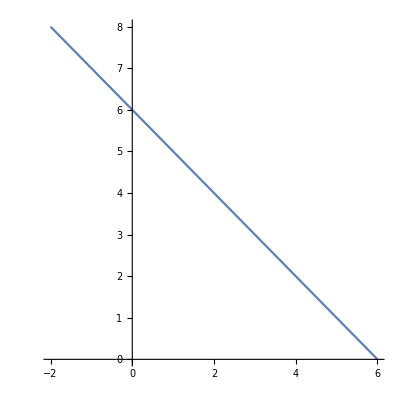

Show::gcomb: Could not combine the graphics objects in Show[FilledPlot[If[x≥0&&x≤4,10,0],{x,-2,6}],,AxesLabel→{x,z},AspectRatio→1].

```mathematica
graycyl=FilledPlot[If[(x≥0)&&(x≤4),10,0],{x,-2,6}]
line=ParametricPlot[{x,6-x},{x,-2,6}]
Show[graycyl,line,AxesLabel->{x,z},AspectRatio->1]
```

```mathematica
Show[FilledPlot[If[xIntegrate[-x+6,{x,0,4},{y,-Sqrt[4-(x-2)^2],Sqrt[4-(x-2)^2]}]≥0&&x≤4,10,0],{x,-2,6}],-Graphics-,AxesLabel->{x,z},AspectRatio->1]
```

```mathematica
Integrate[-x+6,{x,0,4},{y,-Sqrt[4-(x-2)^2],Sqrt[4-(x-2)^2]}]
```

16 π

start of exercise 2
*****
keep in mind that the cylinder has a radius of 2 and is centered at (2,0,0)

a) Suppose that the fluid level in the tank is 7 m on the left edge of the tank (where x=0) and 5 m on the right edge (where x=4). 
***
z=7-(1/2)*x
∫∫∫ dzdydx

inner most integral ∫dz
Integrate[1,{z,0,(7-(1/2)*x)}]
= 7-x/2


 Find the equation of the plane of the liquid, and use a double integral to find the volume of liquid in the tank.  [Hint: you should use a “dy dx” iterated integral, where the bounds on y depend on x, and are given by the equation of the base of the cylinder.]  
 ***
 since we know the x is bounded between 0/4 we can make that the outer most integral and have the dy integral as the middle one 
 ∫∫(7-x/2)dydx
 since we know that y=0 at x=0 and x=4, and y=2&-2 at x=2
 4=y^2+(2-x)^2
 y=±sqrt(4-(2-x)^2)
 Integrate[7-(1/2)*x,{x,0,4},{y,(-1*Sqrt[(4-(2-x)^2)]),(Sqrt[(4-(2-x)^2)])}]
 =24 π
 
 Also find the angle at which the tank is tipped from its upright position.  For consistency, assume that the tank in the Introduction above is tipped at a 0° angle.  [Hint: use a “side elevation” sketch, and use trigonometry to find the angle between your plane and the plane z=5.]
θ=ArcTan[(2/4)]
26.5651˚
or 0.463648 rads

end of part A
*****plane4=ParametricPlot3D[{x,y,7-7x/3},{x,0,3},{y,-2,2}]
Show[cyl,plane4,AxesLabel→{x,y,z},ViewPoint->{0, -3, 0}]

```mathematica
Integrate[1,{z,0,(7-(1/2)*x)}]
```

7-x/2

```mathematica
Integrate[7-(1/2)*x,{x,0,4},{y,(-1*Sqrt[(4-(2-x)^2)]),(Sqrt[(4-(2-x)^2)])}]
```

24 π

```mathematica
ArcTan[2,1]
```

ArcTan[1/2]

```mathematica
N[ArcTan[1/2]]
```

0.463648

```mathematica
N[ArcTan[1/2]/°]
```

26.5651

```mathematica
plane4=ParametricPlot3D[{x,y,7-7x/3},{x,0,3},{y,-2,2}]
Show[cyl,plane4,AxesLabel->{x,y,z},ViewPoint->{0, -3, 0}]
```

-Graphics3D-

-Graphics3D-

****

b) Suppose now that the fluid level is 7 m at the left edge of the tank, but that there isn’t enough fluid to reach the right edge; instead, the fluid covers the base of the tank only out to the plane x=3. 

z=7-(7/3)*x
Inner most integral ∫dz
Integrate[1,{z,0,(7-(7/3)*x)}]
=7-(7 x)/3

Integrate[7-(7/3)*x,{x,0,3},{y,(-1*Sqrt[(4-(2-x)^2)]),(Sqrt[(4-(2-x)^2)])}]
=7 √3+(56 π)/9

θ=ArcTan[(7/3)]
66.8014 °
or 1.1659 rads

end of part B
****

```mathematica
Integrate[1,{z,0,(7-(7/3)*x)}]
```

7-(7 x)/3

```mathematica
Integrate[7-(7/3)*x,{x,0,3},{y,(-1*Sqrt[(4-(2-x)^2)]),(Sqrt[(4-(2-x)^2)])}]
```

7 √3+(56 π)/9

```mathematica
ArcTan[7/3]
```

ArcTan[7/3]

```mathematica
With[{d=N[ArcTan[7/3]/°]},Defer[d °]]
```

66.8014 °

```mathematica
N[ArcTan[7/3]]
```

1.1659

c) Suppose that the tank is tipped so far that the liquid touches both ends of the tank, touching the top (at z=10) out to the plane x=1, and covering the bottom out to the plane x=3.  Find the volume of liquid in the tank using two double integrals.  Explain why you can’t just use one double integral.  Lastly, find the angle at which the tank is tipped from its upright position.

from x=0 to x=1 z=10, then from z=1 to z=3 z=15-5x

∫∫ (∫dz1+∫dz2)dydx = ∫∫∫dz1dydx+∫∫∫dz2dydx
first inner integral is 
Integrate[1,{z,0,(10)}]
=10
second inner integral is
Integrate[1,{z,0,(15)-5*x}]
=15-5 x

then we take a double integral of both elements

dz1
Integrate[10,{x,0,1},{y,(-1*Sqrt[(4-(2-x)^2)]),(Sqrt[(4-(2-x)^2)])}]
=-10 √3+(40 π)/3, approx 24.5674


dz2
Integrate[15-(5*x),{x,1,3},{y,(-1*Sqrt[(4-(2-x)^2)]),(Sqrt[(4-(2-x)^2)])}]
=10 √3+(20 π)/3 approx 38.2645

total volume
=20 π approx 62.8319

θ=ArcTan[(5)]
=78.6901 ° or 1.3734 rads

```mathematica
Integrate[1,{z,0,(10)}]
```

10

```mathematica
Integrate[1,{z,0,(15)-5*x}]
```

15-5 x

```mathematica
Integrate[10,{x,0,1},{y,(-1*Sqrt[(4-(2-x)^2)]),(Sqrt[(4-(2-x)^2)])}]
```

-10 √3+(40 π)/3

```mathematica
N[-10 √3+(40 π)/3]
```

24.5674

```mathematica
Integrate[15-(5*x),{x,1,3},{y,(-1*Sqrt[(4-(2-x)^2)]),(Sqrt[(4-(2-x)^2)])}]
```

10 √3+(20 π)/3

```mathematica
N[10 √3+(20 π)/3]
```

38.2645

```mathematica
(10 √3+(20 π)/3)+(-10 √3+(40 π)/3)
```

20 π

```mathematica
N[20 π]
```

62.8319

```mathematica
ArcTan[5]
```

ArcTan[5]

```mathematica
With[{d=N[ArcTan[5]/°]},Defer[d °]]
```

78.6901 °

```mathematica
N[ArcTan[5]]
```

1.3734

d) Suppose, finally, that the liquid touches the top of the tank out to the plane x=3, and reaches a level of 3 m on the right edge of the tank.  Find the volume of liquid in the tank using two double integrals, and find the angle at which the tank is tipped from its upright position.


from x=0 to 3, z=10
from at x=4, z=3 , in one unit of x z decreased by 7 units

∫∫ (∫dz1+∫dz2)dydx = ∫∫∫dz1dydx+∫∫∫dz2dydx
first inner integral is 
Integrate[1,{z,0,(10)}]
=10
second inner integral is
Integrate[1,{z,0,(31)-7*x}]
=31-7 x

then we take a double integral of both elements

dz1
Integrate[10,{x,0,3},{y,(-1*Sqrt[(4-(2-x)^2)]),(Sqrt[(4-(2-x)^2)])}]
=10 √3+(80 π)/3


dz2
Integrate[31-(7*x),{x,3,4},{y,(-1*Sqrt[(4-(2-x)^2)]),(Sqrt[(4-(2-x)^2)])}]
=-31 √3+(68 π)/3

total volume = -21 √3+(148 π)/3 approx 118.612
θ=ArcTan[(7)]
=81.8699 °
=1.4289 rads

```mathematica
Integrate[1,{z,0,(10)}]
```

10

```mathematica
Integrate[1,{z,0,(31)-7*x}]
```

31-7 x

```mathematica
Integrate[10,{x,0,3},{y,(-1*Sqrt[(4-(2-x)^2)]),(Sqrt[(4-(2-x)^2)])}]
```

10 √3+(80 π)/3

```mathematica
Integrate[31-(7*x),{x,3,4},{y,(-1*Sqrt[(4-(2-x)^2)]),(Sqrt[(4-(2-x)^2)])}]
```

-31 √3+(68 π)/3

```mathematica
(10 √3+(80 π)/3)+(-31 √3+(68 π)/3)
```

-21 √3+(148 π)/3

```mathematica
N[-21 √3+(148 π)/3]
```

118.612

```mathematica
ArcTan[7]
```

ArcTan[7]

```mathematica
With[{d=N[ArcTan[7]/°]},Defer[d °]]
```

81.8699 °

```mathematica
N[ArcTan[7]]
```

1.4289

e) Suppose that our tank is tilted at an angle of 80° from its upright position.  Where could you mark the surface of the tank to indicate when the tank is exactly one-third full?  [Hint: use trigonometry to decide which of the first four exercises most resembles this problem.  Calculate the volume in terms of some unknown variable, and use Mathematica’s FindRoot command, which you can look up in the help browser.]

angle most closely resembles part c 

will have a rate of change of 5.67128 which is closer to the rate of 5 seen in part c then it is to the rate of 7 seen in part d.

max V=π*r^2*h =10*4*π=40π
1/3 volume = 40π/3


∫∫ (∫dz1+∫dz2)dydx = ∫∫∫dz1dydx+∫∫∫dz2dydx
first inner integral is 
Integrate[1,{z,0,(10)}]
=10
second inner integral is
Integrate[1,{z,0,(15.67128)-(5.67128)*x}]
=(15.67128)-5.67128*x

then we take a double integral of both elements

dz1
Integrate[10,{x,0,1},{y,(-1*Sqrt[(4-(2-x)^2)]),(Sqrt[(4-(2-x)^2)])}]


dz2
Integrate[(15.67128)-((5.67128)*x),{x,1,3},{y,(-1*Sqrt[(4-(2-x)^2)]),(Sqrt[(4-(2-x)^2)])}]

at an angle of 80 degrees we can have the water fill from the bottom to the top of the container from x=0 to x=1, then have water go as far as approx x=1.555565m on the bottom of the container to have almost exactly one third (40pi/3) of the volume filled.

```mathematica
Tan[80Degree]
```

Cot[10 °]

```mathematica
N[Cot[10 °]]
```

5.67128

```mathematica
Integrate[1,{z,0,(15.67128)-(5.67128)*x}]
```

15.6713-5.67128 x

```mathematica
Integrate[10,{x,0,1},{y,(-1*Sqrt[(4-(2-x)^2)]),(Sqrt[(4-(2-x)^2)])}]
```

-10 √3+(40 π)/3

```mathematica
N[-10 √3+(40 π)/3]
```

24.5674

```mathematica
Integrate[(15.67128)-((5.67128)*x),{x,1,1.555565},{y,(-1*Sqrt[(4-(2-x)^2)]),(Sqrt[(4-(2-x)^2)])}]
```

17.3205

```mathematica
(40/3)*Pi
```

(40 π)/3

```mathematica
N[(40 π)/3]
```

41.8879

```mathematica
41.88790204786391-24.56739397217514
```

17.3205